```mathematica
Clear[t,u,g,h]
eqns={x'[t]==-I*Δ*x[t]-I*G*y[t],y'[t]==I*Δ*y[t]+I*G*x[t],x[0]==a,y[0]==b};
sol=DSolve[eqns,{x,y},t]
Plot[{Re[x[t]/.sol],y[t]/.sol},{t,-10,10}]
```

{{x→Function[{t},(ⅇ^(-ⅈ t √(-G^2+Δ^2)) (b G-b ⅇ^(2 ⅈ t √(-G^2+Δ^2)) G+a Δ-a ⅇ^(2 ⅈ t √(-G^2+Δ^2)) Δ+a √(-G^2+Δ^2)+a ⅇ^(2 ⅈ t √(-G^2+Δ^2)) √(-G^2+Δ^2)))/(2 √(-G^2+Δ^2))],y→Function[{t},(ⅇ^(-ⅈ t √(-G^2+Δ^2)) (-a G+a ⅇ^(2 ⅈ t √(-G^2+Δ^2)) G-b Δ+b ⅇ^(2 ⅈ t √(-G^2+Δ^2)) Δ+b √(-G^2+Δ^2)+b ⅇ^(2 ⅈ t √(-G^2+Δ^2)) √(-G^2+Δ^2)))/(2 √(-G^2+Δ^2))]}}

-Graphics-

```mathematica
f[x_,y_,w_,z_,t_,S_]:=-I*Δ*x*S-I*S*χ*Exp[-I*ω*t*S]*(y+w+Exp[-I*ω*t*S]*z);
eqns={
x'[t]==f[x[t],yc[t],zc[t],wc[t],t,1],
y'[t]==f[y[t],xc[t],0,vc[t],t,1],
z'[t]==f[z[t],xc[t],0,uc[t],t,1],
w'[t]==f[w[t],vc[t],uc[t],xc[t],t,1],
v'[t]==f[v[t],wc[t],0,yc[t],t,1],
u'[t]==f[u[t],wc[t],0,zc[t],t,1],
xc'[t]==f[xc[t],y[t],z[t],w[t],t,0],
yc'[t]==f[yc[t],x[t],0,v[t],t,0],
zc'[t]==f[zc[t],x[t],0,u[t],t,0],
wc'[t]==f[wc[t],v[t],u[t],x[t],t,0],
vc'[t]==f[vc[t],w[t],0,y[t],t,0],
uc'[t]==f[uc[t],w[t],0,z[t],t,0],
x[0]==a,y[0]==b,z[0]==d,w[0]==g,v[0]==h,u[0]==l,wc[0]==gc};
sol=DSolve[eqns,{x,y,z,w,v,u,xc,yc,zc,wc,vc,uc},t]
```

{{wc→Function[{t},gc],yc→Function[{t},-((Δ-2 ω) (h Δ+gc χ-h ω-Δ C[3]+ω C[3]))/(χ (Δ-ω))],v→Function[{t},-(ⅇ^(-ⅈ t Δ) (-ⅇ^(ⅈ t (Δ-2 ω)) h Δ-ⅇ^(ⅈ t (Δ-2 ω)) gc χ+ⅇ^(ⅈ t (Δ-ω)) gc χ+ⅇ^(ⅈ t (Δ-2 ω)) h ω-Δ C[3]+ⅇ^(ⅈ t (Δ-2 ω)) Δ C[3]+ω C[3]-ⅇ^(ⅈ t (Δ-2 ω)) ω C[3]))/(Δ-ω)],zc→Function[{t},-((Δ-2 ω) (l Δ+gc χ-l ω-Δ C[5]+ω C[5]))/(χ (Δ-ω))],u→Function[{t},-(ⅇ^(-ⅈ t Δ) (-ⅇ^(ⅈ t (Δ-2 ω)) l Δ-ⅇ^(ⅈ t (Δ-2 ω)) gc χ+ⅇ^(ⅈ t (Δ-ω)) gc χ+ⅇ^(ⅈ t (Δ-2 ω)) l ω-Δ C[5]+ⅇ^(ⅈ t (Δ-2 ω)) Δ C[5]+ω C[5]-ⅇ^(ⅈ t (Δ-2 ω)) ω C[5]))/(Δ-ω)],x→Function[{t},1/((Δ-2 ω) (Δ-ω)^2)ⅇ^(-ⅈ t Δ) (a Δ^3-h Δ^3+ⅇ^(ⅈ t (Δ-ω)) h Δ^3-l Δ^3+ⅇ^(ⅈ t (Δ-ω)) l Δ^3-gc Δ^2 χ-ⅇ^(ⅈ t (Δ-2 ω)) gc Δ^2 χ+2 ⅇ^(ⅈ t (Δ-ω)) gc Δ^2 χ-4 a Δ^2 ω+5 h Δ^2 ω-5 ⅇ^(ⅈ t (Δ-ω)) h Δ^2 ω+5 l Δ^2 ω-5 ⅇ^(ⅈ t (Δ-ω)) l Δ^2 ω+6 gc Δ χ ω+2 ⅇ^(ⅈ t (Δ-2 ω)) gc Δ χ ω-8 ⅇ^(ⅈ t (Δ-ω)) gc Δ χ ω+5 a Δ ω^2-8 h Δ ω^2+8 ⅇ^(ⅈ t (Δ-ω)) h Δ ω^2-8 l Δ ω^2+8 ⅇ^(ⅈ t (Δ-ω)) l Δ ω^2-7 gc χ ω^2-ⅇ^(ⅈ t (Δ-2 ω)) gc χ ω^2+8 ⅇ^(ⅈ t (Δ-ω)) gc χ ω^2-2 a ω^3+4 h ω^3-4 ⅇ^(ⅈ t (Δ-ω)) h ω^3+4 l ω^3-4 ⅇ^(ⅈ t (Δ-ω)) l ω^3+Δ^3 C[3]-ⅇ^(ⅈ t (Δ-ω)) Δ^3 C[3]-5 Δ^2 ω C[3]+5 ⅇ^(ⅈ t (Δ-ω)) Δ^2 ω C[3]+8 Δ ω^2 C[3]-8 ⅇ^(ⅈ t (Δ-ω)) Δ ω^2 C[3]-4 ω^3 C[3]+4 ⅇ^(ⅈ t (Δ-ω)) ω^3 C[3]+Δ^3 C[5]-ⅇ^(ⅈ t (Δ-ω)) Δ^3 C[5]-5 Δ^2 ω C[5]+5 ⅇ^(ⅈ t (Δ-ω)) Δ^2 ω C[5]+8 Δ ω^2 C[5]-8 ⅇ^(ⅈ t (Δ-ω)) Δ ω^2 C[5]-4 ω^3 C[5]+4 ⅇ^(ⅈ t (Δ-ω)) ω^3 C[5])],uc→Function[{t},1/(χ (Δ^2-6 Δ ω+7 ω^2))(b Δ^3-g Δ^3-6 b Δ^2 ω+2 d Δ^2 ω+5 g Δ^2 ω+12 b Δ ω^2-7 d Δ ω^2-8 g Δ ω^2-8 b ω^3+6 d ω^3+4 g ω^3+Δ^3 C[10]-5 Δ^2 ω C[10]+8 Δ ω^2 C[10]-4 ω^3 C[10]-Δ^3 C[11]+6 Δ^2 ω C[11]-12 Δ ω^2 C[11]+8 ω^3 C[11]-2 Δ^2 ω C[12]+7 Δ ω^2 C[12]-6 ω^3 C[12])],vc→Function[{t},1/(χ (Δ^2-6 Δ ω+7 ω^2))(d Δ^3-g Δ^3+2 b Δ^2 ω-6 d Δ^2 ω+5 g Δ^2 ω-7 b Δ ω^2+12 d Δ ω^2-8 g Δ ω^2+6 b ω^3-8 d ω^3+4 g ω^3+Δ^3 C[10]-5 Δ^2 ω C[10]+8 Δ ω^2 C[10]-4 ω^3 C[10]-2 Δ^2 ω C[11]+7 Δ ω^2 C[11]-6 ω^3 C[11]-Δ^3 C[12]+6 Δ^2 ω C[12]-12 Δ ω^2 C[12]+8 ω^3 C[12])],xc→Function[{t},-((Δ-2 ω) (Δ-ω) (b Δ+d Δ-g Δ-2 b ω-2 d ω+g ω+Δ C[10]-ω C[10]-Δ C[11]+2 ω C[11]-Δ C[12]+2 ω C[12]))/(χ (Δ^2-6 Δ ω+7 ω^2))],w→Function[{t},1/(Δ^2-6 Δ ω+7 ω^2)ⅇ^(-ⅈ t Δ) (b ⅇ^(ⅈ t (Δ-2 ω)) Δ^2+d ⅇ^(ⅈ t (Δ-2 ω)) Δ^2-b ⅇ^(ⅈ t (Δ-ω)) Δ^2-d ⅇ^(ⅈ t (Δ-ω)) Δ^2-ⅇ^(ⅈ t (Δ-2 ω)) g Δ^2+2 ⅇ^(ⅈ t (Δ-ω)) g Δ^2-3 b ⅇ^(ⅈ t (Δ-2 ω)) Δ ω-3 d ⅇ^(ⅈ t (Δ-2 ω)) Δ ω+3 b ⅇ^(ⅈ t (Δ-ω)) Δ ω+3 d ⅇ^(ⅈ t (Δ-ω)) Δ ω+2 ⅇ^(ⅈ t (Δ-2 ω)) g Δ ω-8 ⅇ^(ⅈ t (Δ-ω)) g Δ ω+2 b ⅇ^(ⅈ t (Δ-2 ω)) ω^2+2 d ⅇ^(ⅈ t (Δ-2 ω)) ω^2-2 b ⅇ^(ⅈ t (Δ-ω)) ω^2-2 d ⅇ^(ⅈ t (Δ-ω)) ω^2-ⅇ^(ⅈ t (Δ-2 ω)) g ω^2+8 ⅇ^(ⅈ t (Δ-ω)) g ω^2+Δ^2 C[10]+ⅇ^(ⅈ t (Δ-2 ω)) Δ^2 C[10]-2 ⅇ^(ⅈ t (Δ-ω)) Δ^2 C[10]-6 Δ ω C[10]-2 ⅇ^(ⅈ t (Δ-2 ω)) Δ ω C[10]+8 ⅇ^(ⅈ t (Δ-ω)) Δ ω C[10]+7 ω^2 C[10]+ⅇ^(ⅈ t (Δ-2 ω)) ω^2 C[10]-8 ⅇ^(ⅈ t (Δ-ω)) ω^2 C[10]-ⅇ^(ⅈ t (Δ-2 ω)) Δ^2 C[11]+ⅇ^(ⅈ t (Δ-ω)) Δ^2 C[11]+3 ⅇ^(ⅈ t (Δ-2 ω)) Δ ω C[11]-3 ⅇ^(ⅈ t (Δ-ω)) Δ ω C[11]-2 ⅇ^(ⅈ t (Δ-2 ω)) ω^2 C[11]+2 ⅇ^(ⅈ t (Δ-ω)) ω^2 C[11]-ⅇ^(ⅈ t (Δ-2 ω)) Δ^2 C[12]+ⅇ^(ⅈ t (Δ-ω)) Δ^2 C[12]+3 ⅇ^(ⅈ t (Δ-2 ω)) Δ ω C[12]-3 ⅇ^(ⅈ t (Δ-ω)) Δ ω C[12]-2 ⅇ^(ⅈ t (Δ-2 ω)) ω^2 C[12]+2 ⅇ^(ⅈ t (Δ-ω)) ω^2 C[12])],y→Function[{t},1/(Δ^2-6 Δ ω+7 ω^2)ⅇ^(-ⅈ t Δ) (-d ⅇ^(ⅈ t (Δ-2 ω)) Δ^2+b ⅇ^(ⅈ t (Δ-ω)) Δ^2+d ⅇ^(ⅈ t (Δ-ω)) Δ^2+ⅇ^(ⅈ t (Δ-2 ω)) g Δ^2-ⅇ^(ⅈ t (Δ-ω)) g Δ^2-2 b ⅇ^(ⅈ t (Δ-2 ω)) Δ ω+4 d ⅇ^(ⅈ t (Δ-2 ω)) Δ ω-4 b ⅇ^(ⅈ t (Δ-ω)) Δ ω-4 d ⅇ^(ⅈ t (Δ-ω)) Δ ω-3 ⅇ^(ⅈ t (Δ-2 ω)) g Δ ω+3 ⅇ^(ⅈ t (Δ-ω)) g Δ ω+3 b ⅇ^(ⅈ t (Δ-2 ω)) ω^2-4 d ⅇ^(ⅈ t (Δ-2 ω)) ω^2+4 b ⅇ^(ⅈ t (Δ-ω)) ω^2+4 d ⅇ^(ⅈ t (Δ-ω)) ω^2+2 ⅇ^(ⅈ t (Δ-2 ω)) g ω^2-2 ⅇ^(ⅈ t (Δ-ω)) g ω^2-ⅇ^(ⅈ t (Δ-2 ω)) Δ^2 C[10]+ⅇ^(ⅈ t (Δ-ω)) Δ^2 C[10]+3 ⅇ^(ⅈ t (Δ-2 ω)) Δ ω C[10]-3 ⅇ^(ⅈ t (Δ-ω)) Δ ω C[10]-2 ⅇ^(ⅈ t (Δ-2 ω)) ω^2 C[10]+2 ⅇ^(ⅈ t (Δ-ω)) ω^2 C[10]+Δ^2 C[11]-ⅇ^(ⅈ t (Δ-ω)) Δ^2 C[11]-6 Δ ω C[11]+2 ⅇ^(ⅈ t (Δ-2 ω)) Δ ω C[11]+4 ⅇ^(ⅈ t (Δ-ω)) Δ ω C[11]+7 ω^2 C[11]-3 ⅇ^(ⅈ t (Δ-2 ω)) ω^2 C[11]-4 ⅇ^(ⅈ t (Δ-ω)) ω^2 C[11]+ⅇ^(ⅈ t (Δ-2 ω)) Δ^2 C[12]-ⅇ^(ⅈ t (Δ-ω)) Δ^2 C[12]-4 ⅇ^(ⅈ t (Δ-2 ω)) Δ ω C[12]+4 ⅇ^(ⅈ t (Δ-ω)) Δ ω C[12]+4 ⅇ^(ⅈ t (Δ-2 ω)) ω^2 C[12]-4 ⅇ^(ⅈ t (Δ-ω)) ω^2 C[12])],z→Function[{t},1/(Δ^2-6 Δ ω+7 ω^2)ⅇ^(-ⅈ t Δ) (-b ⅇ^(ⅈ t (Δ-2 ω)) Δ^2+b ⅇ^(ⅈ t (Δ-ω)) Δ^2+d ⅇ^(ⅈ t (Δ-ω)) Δ^2+ⅇ^(ⅈ t (Δ-2 ω)) g Δ^2-ⅇ^(ⅈ t (Δ-ω)) g Δ^2+4 b ⅇ^(ⅈ t (Δ-2 ω)) Δ ω-2 d ⅇ^(ⅈ t (Δ-2 ω)) Δ ω-4 b ⅇ^(ⅈ t (Δ-ω)) Δ ω-4 d ⅇ^(ⅈ t (Δ-ω)) Δ ω-3 ⅇ^(ⅈ t (Δ-2 ω)) g Δ ω+3 ⅇ^(ⅈ t (Δ-ω)) g Δ ω-4 b ⅇ^(ⅈ t (Δ-2 ω)) ω^2+3 d ⅇ^(ⅈ t (Δ-2 ω)) ω^2+4 b ⅇ^(ⅈ t (Δ-ω)) ω^2+4 d ⅇ^(ⅈ t (Δ-ω)) ω^2+2 ⅇ^(ⅈ t (Δ-2 ω)) g ω^2-2 ⅇ^(ⅈ t (Δ-ω)) g ω^2-ⅇ^(ⅈ t (Δ-2 ω)) Δ^2 C[10]+ⅇ^(ⅈ t (Δ-ω)) Δ^2 C[10]+3 ⅇ^(ⅈ t (Δ-2 ω)) Δ ω C[10]-3 ⅇ^(ⅈ t (Δ-ω)) Δ ω C[10]-2 ⅇ^(ⅈ t (Δ-2 ω)) ω^2 C[10]+2 ⅇ^(ⅈ t (Δ-ω)) ω^2 C[10]+ⅇ^(ⅈ t (Δ-2 ω)) Δ^2 C[11]-ⅇ^(ⅈ t (Δ-ω)) Δ^2 C[11]-4 ⅇ^(ⅈ t (Δ-2 ω)) Δ ω C[11]+4 ⅇ^(ⅈ t (Δ-ω)) Δ ω C[11]+4 ⅇ^(ⅈ t (Δ-2 ω)) ω^2 C[11]-4 ⅇ^(ⅈ t (Δ-ω)) ω^2 C[11]+Δ^2 C[12]-ⅇ^(ⅈ t (Δ-ω)) Δ^2 C[12]-6 Δ ω C[12]+2 ⅇ^(ⅈ t (Δ-2 ω)) Δ ω C[12]+4 ⅇ^(ⅈ t (Δ-ω)) Δ ω C[12]+7 ω^2 C[12]-3 ⅇ^(ⅈ t (Δ-2 ω)) ω^2 C[12]-4 ⅇ^(ⅈ t (Δ-ω)) ω^2 C[12])]}}

```mathematica
{u,uc,v,vc,w,wc,x,xc,y,yc,z,zc}/.sol
```

{{Function[{t},1/((Δ-2 ω)^2 (Δ-ω))ⅇ^(-ⅈ t Δ) (a ⅇ^(ⅈ t (Δ-2 ω)) Δ^3-ⅇ^(ⅈ t (Δ-2 ω)) h Δ^3-4 a ⅇ^(ⅈ t (Δ-2 ω)) Δ^2 ω+5 ⅇ^(ⅈ t (Δ-2 ω)) h Δ^2 ω+5 a ⅇ^(ⅈ t (Δ-2 ω)) Δ ω^2-8 ⅇ^(ⅈ t (Δ-2 ω)) h Δ ω^2-2 a ⅇ^(ⅈ t (Δ-2 ω)) ω^3+4 ⅇ^(ⅈ t (Δ-2 ω)) h ω^3-ⅇ^(ⅈ t (Δ-ω)) Δ^2 χ C[1]+2 ⅇ^(ⅈ t (Δ-2 ω)) Δ χ ω C[1]+4 ⅇ^(ⅈ t (Δ-ω)) Δ χ ω C[1]-3 ⅇ^(ⅈ t (Δ-2 ω)) χ ω^2 C[1]-4 ⅇ^(ⅈ t (Δ-ω)) χ ω^2 C[1]+ⅇ^(ⅈ t (Δ-2 ω)) Δ^3 C[3]-5 ⅇ^(ⅈ t (Δ-2 ω)) Δ^2 ω C[3]+8 ⅇ^(ⅈ t (Δ-2 ω)) Δ ω^2 C[3]-4 ⅇ^(ⅈ t (Δ-2 ω)) ω^3 C[3]+Δ^3 C[5]-5 Δ^2 ω C[5]+8 Δ ω^2 C[5]-4 ω^3 C[5]-ⅇ^(ⅈ t (Δ-2 ω)) Δ^3 C[6]+4 ⅇ^(ⅈ t (Δ-2 ω)) Δ^2 ω C[6]-5 ⅇ^(ⅈ t (Δ-2 ω)) Δ ω^2 C[6]+2 ⅇ^(ⅈ t (Δ-2 ω)) ω^3 C[6])],Function[{t},C[7]],Function[{t},-(ⅇ^(-ⅈ t Δ) (-ⅇ^(ⅈ t (Δ-2 ω)) h Δ+ⅇ^(ⅈ t (Δ-2 ω)) h ω-ⅇ^(ⅈ t (Δ-2 ω)) χ C[1]+ⅇ^(ⅈ t (Δ-ω)) χ C[1]-Δ C[3]+ⅇ^(ⅈ t (Δ-2 ω)) Δ C[3]+ω C[3]-ⅇ^(ⅈ t (Δ-2 ω)) ω C[3]))/(Δ-ω)],Function[{t},(-b Δ^2+3 b Δ ω-2 b ω^2-Δ χ C[9]+2 χ ω C[9]+Δ^2 C[11]-3 Δ ω C[11]+2 ω^2 C[11])/(χ (Δ-ω))],Function[{t},1/((Δ-2 ω) (Δ-ω)^2)ⅇ^(-ⅈ t Δ) (-b Δ^3+b ⅇ^(ⅈ t (Δ-ω)) Δ^3+g Δ^3+5 b Δ^2 ω-5 b ⅇ^(ⅈ t (Δ-ω)) Δ^2 ω-4 g Δ^2 ω-8 b Δ ω^2+8 b ⅇ^(ⅈ t (Δ-ω)) Δ ω^2+5 g Δ ω^2+4 b ω^3-4 b ⅇ^(ⅈ t (Δ-ω)) ω^3-2 g ω^3+Δ^2 χ C[7]-ⅇ^(ⅈ t (Δ-ω)) Δ^2 χ C[7]-3 Δ χ ω C[7]+3 ⅇ^(ⅈ t (Δ-ω)) Δ χ ω C[7]+2 χ ω^2 C[7]-2 ⅇ^(ⅈ t (Δ-ω)) χ ω^2 C[7]-ⅇ^(ⅈ t (Δ-2 ω)) Δ^2 χ C[9]+ⅇ^(ⅈ t (Δ-ω)) Δ^2 χ C[9]+2 Δ χ ω C[9]+2 ⅇ^(ⅈ t (Δ-2 ω)) Δ χ ω C[9]-4 ⅇ^(ⅈ t (Δ-ω)) Δ χ ω C[9]-3 χ ω^2 C[9]-ⅇ^(ⅈ t (Δ-2 ω)) χ ω^2 C[9]+4 ⅇ^(ⅈ t (Δ-ω)) χ ω^2 C[9]+Δ^3 C[11]-ⅇ^(ⅈ t (Δ-ω)) Δ^3 C[11]-5 Δ^2 ω C[11]+5 ⅇ^(ⅈ t (Δ-ω)) Δ^2 ω C[11]+8 Δ ω^2 C[11]-8 ⅇ^(ⅈ t (Δ-ω)) Δ ω^2 C[11]-4 ω^3 C[11]+4 ⅇ^(ⅈ t (Δ-ω)) ω^3 C[11])],Function[{t},C[1]],Function[{t},-(ⅇ^(-ⅈ t Δ) (-a ⅇ^(ⅈ t (Δ-ω)) Δ+2 a ⅇ^(ⅈ t (Δ-ω)) ω+ⅇ^(ⅈ t (Δ-2 ω)) χ C[1]-ⅇ^(ⅈ t (Δ-ω)) χ C[1]-Δ C[6]+ⅇ^(ⅈ t (Δ-ω)) Δ C[6]+2 ω C[6]-2 ⅇ^(ⅈ t (Δ-ω)) ω C[6]))/(Δ-2 ω)],Function[{t},C[9]],Function[{t},-(ⅇ^(-ⅈ t Δ) (-b ⅇ^(ⅈ t (Δ-2 ω)) Δ+b ⅇ^(ⅈ t (Δ-2 ω)) ω-ⅇ^(ⅈ t (Δ-2 ω)) χ C[9]+ⅇ^(ⅈ t (Δ-ω)) χ C[9]-Δ C[11]+ⅇ^(ⅈ t (Δ-2 ω)) Δ C[11]+ω C[11]-ⅇ^(ⅈ t (Δ-2 ω)) ω C[11]))/(Δ-ω)],Function[{t},(-h Δ^2+3 h Δ ω-2 h ω^2-Δ χ C[1]+2 χ ω C[1]+Δ^2 C[3]-3 Δ ω C[3]+2 ω^2 C[3])/(χ (Δ-ω))],Function[{t},1/((Δ-2 ω) (Δ-ω))ⅇ^(-ⅈ t Δ) (d Δ^2-3 d Δ ω+2 d ω^2+Δ χ C[7]-ⅇ^(ⅈ t (Δ-2 ω)) Δ χ C[7]-χ ω C[7]+ⅇ^(ⅈ t (Δ-2 ω)) χ ω C[7]+Δ χ C[9]-ⅇ^(ⅈ t (Δ-ω)) Δ χ C[9]-2 χ ω C[9]+2 ⅇ^(ⅈ t (Δ-ω)) χ ω C[9])],Function[{t},1/(χ (Δ-2 ω) (Δ-ω))(-a Δ^3+h Δ^3+4 a Δ^2 ω-5 h Δ^2 ω-5 a Δ ω^2+8 h Δ ω^2+2 a ω^3-4 h ω^3-2 Δ χ ω C[1]+3 χ ω^2 C[1]-Δ^3 C[3]+5 Δ^2 ω C[3]-8 Δ ω^2 C[3]+4 ω^3 C[3]+Δ^3 C[6]-4 Δ^2 ω C[6]+5 Δ ω^2 C[6]-2 ω^3 C[6])]}}

```mathematica
FullSimplify[(ⅇ^(-ⅈ t √(-G^2+Δ^2)) (-a G+a ⅇ^(2 ⅈ t √(-G^2+Δ^2)) G-b Δ+b ⅇ^(2 ⅈ t √(-G^2+Δ^2)) Δ+b √(-G^2+Δ^2)+b ⅇ^(2 ⅈ t √(-G^2+Δ^2)) √(-G^2+Δ^2)))/(2 √(-G^2+Δ^2))]
```

b Cos[t √(-G^2+Δ^2)]+(ⅈ (a G+b Δ) Sin[t √(-G^2+Δ^2)])/(√(-G^2+Δ^2))

```mathematica
FullSimplify[1/((Δ-2 ω) (Δ-ω)^2)ⅇ^(-ⅈ t Δ) (a Δ^3-h Δ^3+ⅇ^(ⅈ t (Δ-ω)) h Δ^3-l Δ^3+ⅇ^(ⅈ t (Δ-ω)) l Δ^3-gc Δ^2 χ-ⅇ^(ⅈ t (Δ-2 ω)) gc Δ^2 χ+2 ⅇ^(ⅈ t (Δ-ω)) gc Δ^2 χ-4 a Δ^2 ω+5 h Δ^2 ω-5 ⅇ^(ⅈ t (Δ-ω)) h Δ^2 ω+5 l Δ^2 ω-5 ⅇ^(ⅈ t (Δ-ω)) l Δ^2 ω+6 gc Δ χ ω+2 ⅇ^(ⅈ t (Δ-2 ω)) gc Δ χ ω-8 ⅇ^(ⅈ t (Δ-ω)) gc Δ χ ω+5 a Δ ω^2-8 h Δ ω^2+8 ⅇ^(ⅈ t (Δ-ω)) h Δ ω^2-8 l Δ ω^2+8 ⅇ^(ⅈ t (Δ-ω)) l Δ ω^2-7 gc χ ω^2-ⅇ^(ⅈ t (Δ-2 ω)) gc χ ω^2+8 ⅇ^(ⅈ t (Δ-ω)) gc χ ω^2-2 a ω^3+4 h ω^3-4 ⅇ^(ⅈ t (Δ-ω)) h ω^3+4 l ω^3-4 ⅇ^(ⅈ t (Δ-ω)) l ω^3+Δ^3 C[3]-ⅇ^(ⅈ t (Δ-ω)) Δ^3 C[3]-5 Δ^2 ω C[3]+5 ⅇ^(ⅈ t (Δ-ω)) Δ^2 ω C[3]+8 Δ ω^2 C[3]-8 ⅇ^(ⅈ t (Δ-ω)) Δ ω^2 C[3]-4 ω^3 C[3]+4 ⅇ^(ⅈ t (Δ-ω)) ω^3 C[3]+Δ^3 C[5]-ⅇ^(ⅈ t (Δ-ω)) Δ^3 C[5]-5 Δ^2 ω C[5]+5 ⅇ^(ⅈ t (Δ-ω)) Δ^2 ω C[5]+8 Δ ω^2 C[5]-8 ⅇ^(ⅈ t (Δ-ω)) Δ ω^2 C[5]-4 ω^3 C[5]+4 ⅇ^(ⅈ t (Δ-ω)) ω^3 C[5])]
```

1/((Δ-2 ω) (Δ-ω)^2)ⅇ^(-ⅈ t Δ) (-h Δ^3-l Δ^3-gc Δ^2 χ-ⅇ^(ⅈ t (Δ-2 ω)) gc Δ^2 χ+a (Δ-2 ω) (Δ-ω)^2+5 h Δ^2 ω+5 l Δ^2 ω+6 gc Δ χ ω+2 ⅇ^(ⅈ t (Δ-2 ω)) gc Δ χ ω-8 h Δ ω^2-8 l Δ ω^2-7 gc χ ω^2-ⅇ^(ⅈ t (Δ-2 ω)) gc χ ω^2+4 h ω^3+4 l ω^3+Δ^3 C[3]-5 Δ^2 ω C[3]+8 Δ ω^2 C[3]-4 ω^3 C[3]+ⅇ^(ⅈ t (Δ-ω)) (Δ-2 ω)^2 (2 gc χ+(Δ-ω) (h+l-C[3]-C[5]))+Δ^3 C[5]-5 Δ^2 ω C[5]+8 Δ ω^2 C[5]-4 ω^3 C[5])

```mathematica
(-2 as-A av-at B+√(4 as^2+4 A as av+A^2 av^2+4 as at B+2 A at av B+at^2 B^2-8 asd B Ct-8 A asd Cv)+4 asd fs)/(4 asd)/.{as->1,av->0.2,at->0.1,B->0.05,Cv->0.33,Ct->0.23,asd->0.01}
```

25. (-2.005-0.2 A+√(4.01911+0.7756 A+0.04 A^2)+0.04 fs)

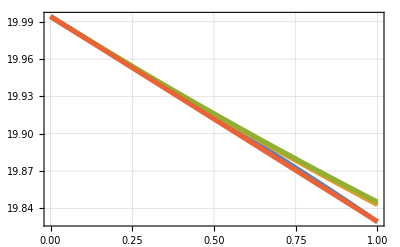

```mathematica
as=1;av=0.2;at=0.1;B=0.05;Cv=0.33;Ct=0.23;asd=0.1;avd=1.01;atd=0.01;fs=20;
Plot[{1/(2 (2 asd+A avd+atd B))(-2 as-A av-at B+√(4 as^2+4 A as av+A^2 av^2+4 as at B+2 A at av B+at^2 B^2-8 asd B Ct-4 A avd B Ct-4 atd B^2 Ct-8 A asd Cv-4 A^2 avd Cv-4 A atd B Cv)+4 asd fs+2 A avd fs+2 atd B fs),1/(4 asd)(-2 as-A av-at B+√(4 as^2+4 A as av+A^2 av^2+4 as at B+2 A at av B+at^2 B^2-8 asd B Ct-8 A asd Cv)+4 asd fs),(-B Ct-A Cv+2 as fs+A av fs+at B fs)/(2 as+A av+at B),(-B Ct-A Cv+2 as fs)/(2 as)},{A,0,1}]
```

```mathematica
Clear[as,av,at,B,Cv,Ct,asd,fs]
```

```mathematica
sol=DSolve[{0==as*(fto[fs]-fs)+A/2*av*(fto[fs]-fs)+B/2*at*(fto[fs]-fs)+A/2*Cv+B/2*Ct+asd*(fto[fs]-fs)^2+avd*A/2*(fto[fs]-fs)^2+atd*B/2*(fto[fs]-fs)^2},{fto},fs]
```

{{fto→Function[{fs},1/(2 (2 asd+A avd+atd B))(-2 as-A av-at B-√(4 as^2+4 A as av+A^2 av^2+4 as at B+2 A at av B+at^2 B^2-8 asd B Ct-4 A avd B Ct-4 atd B^2 Ct-8 A asd Cv-4 A^2 avd Cv-4 A atd B Cv)+4 asd fs+2 A avd fs+2 atd B fs)]},{fto→Function[{fs},1/(2 (2 asd+A avd+atd B))(-2 as-A av-at B+√(4 as^2+4 A as av+A^2 av^2+4 as at B+2 A at av B+at^2 B^2-8 asd B Ct-4 A avd B Ct-4 atd B^2 Ct-8 A asd Cv-4 A^2 avd Cv-4 A atd B Cv)+4 asd fs+2 A avd fs+2 atd B fs)]}}

```mathematica
FullSimplify[{(-2 as-A av-at B+√(4 as^2+4 A as av+A^2 av^2+4 as at B+2 A at av B+at^2 B^2-8 asd B Ct-8 A asd Cv)+4 asd fs)/(4 asd),(-B Ct-A Cv+2 as fs+A av fs+at B fs)/(2 as+A av+at B)}/.{asd->0}]
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

```mathematica
ExpandNumerator[-(2 as+A av+at B-√(4 as^2+4 A as av+A^2 av^2+4 as at B+2 A at av B+at^2 B^2-8 asd B Ct-8 A asd Cv)-4 asd fs)/(4 asd)]
```

(-2 as-A av-at B+√(4 as^2+4 A as av+A^2 av^2+4 as at B+2 A at av B+at^2 B^2-8 asd B Ct-8 A asd Cv)+4 asd fs)/(4 asd)

```mathematica
Simplify[(-2 as-A av-at B+√(4 as^2+4 A as av+A^2 av^2+4 as at B+2 A at av B+at^2 B^2-8 asd B Ct-8 A asd Cv)+4 asd fs)/(4 asd)]
```

-(2 as+A av+at B-√(4 as^2+4 A as av+A^2 av^2+4 as at B+2 A at av B+at^2 B^2-8 asd B Ct-8 A asd Cv)-4 asd fs)/(4 asd)

```mathematica
Expand[-(2 as+A av+at B-√(4 as^2+4 A as av+A^2 av^2+4 as at B+2 A at av B+at^2 B^2-8 asd B Ct-8 A asd Cv)-4 asd fs)/(4 asd)]
```

-as/(2 asd)-(A av)/(4 asd)-(at B)/(4 asd)+(√(4 as^2+4 A as av+A^2 av^2+4 as at B+2 A at av B+at^2 B^2-8 asd B Ct-8 A asd Cv))/(4 asd)+fs

```mathematica
FullSimplify[4 as^2+4 A as av+A^2 av^2+4 as at B+2 A at av B+at^2 B^2-8 asd B Ct-8 A asd Cv]/.{asd->0}
```

4 as^2+A^2 av^2+2 A at av B+at^2 B^2+4 as (A av+at B)

```mathematica
Limit[(-2 as-A av-at B+√(4 as^2+4 A as av+A^2 av^2+4 as at B+2 A at av B+at^2 B^2-8 asd B Ct-8 A asd Cv)+4 asd fs)/(4 asd),asd->0.001]
```

250. (-2 as-A av-1. at B+√(4 as^2+4 A as av+A^2 av^2+4 as at B+2 A at av B+at^2 B^2-0.008 B Ct-0.008 A Cv)+0.004 fs)

```mathematica
{1,2}^2*{1,1}
```

{1,4}

```mathematica
Erf[100000]*Sqrt[2*Pi]
```

√(2 π) Erf[100000]

```mathematica
λ
```

λ

```mathematica
ClearAll[λ]
```

```mathematica
FullSimplify[Sum[l^(2*(n))*(n*n),{n,0,Infinity}]*(1-l^2)]
```

(l^2+l^4)/((-1+l^2)^2)

```mathematica
Sum[l^(2*(n))*(n),{n,0,Infinity}]*(1-l^2)^2
```

(l^2 (1-l^2)^2)/((-1+l^2)^2)

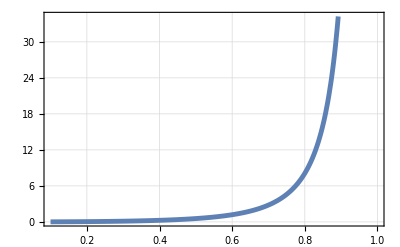

```mathematica
Plot[(l^2+l^4)/((-1+l^2)^2),{l,0.1,1}]
```

```mathematica
FullSimplify[Sum[l^(2*(n))*(n*n),{n,0,Infinity}]/Sum[l^(2*(n))*(n),{n,0,Infinity}]^2*1/(1-l^2)]
```

1+1/l^2

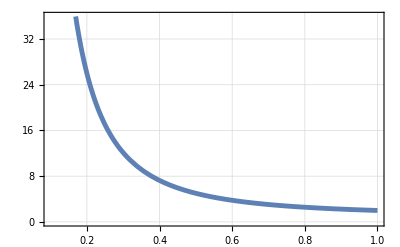

```mathematica
Plot[1+1/l^2,{l,0.1,1}]
```

```mathematica
Clear[R]
b1=Sqrt[T2]*c1+I*Sqrt[R2]*c2;
b2=Exp[I*θ]*(Sqrt[T2]*c2+I*Sqrt[R2]*c1);
FullSimplify[Sqrt[T]*b1+I*Sqrt[R]*b2]
```

√T (ⅈ c2 √R2+c1 √T2)+ⅇ^(ⅈ θ) √R (-c1 √R2+ⅈ c2 √T2)

```mathematica
Collect[√T (ⅈ c2 √R2+c1 √T2)+ⅇ^(ⅈ θ) √R (-c1 √R2+ⅈ c2 √T2),c1]
```

ⅈ c2 √R2 √T+c1 (-ⅇ^(ⅈ θ) √R √R2+√T √T2)+ⅈ c2 ⅇ^(ⅈ θ) √R √T2

```mathematica
Abs[(-ⅇ^(ⅈ θ) √R √R2+√T √T2)]^2
```

Abs[-ⅇ^(ⅈ θ) √R √R2+√T √T2]^2

```mathematica
FullSimplify[Abs[-ⅇ^(ⅈ θ) √R √R2+√T √T2]^2]
```

Abs[ⅇ^(ⅈ θ) √R √R2-√T √T2]^2

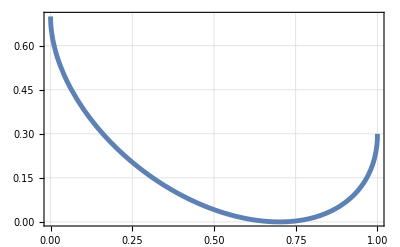

```mathematica
R=0.7;
T=1-R;
Plot[R*(1-x)+T*x-2*Sqrt[R*(1-x)*T*x],{x,0,1}]
```